## Setup

```mathematica
Clear@Evaluate[Context[]<>"*"];
SetDirectory@NotebookDirectory[];
```

```mathematica
GetZFileBCP[𝓈_Integer?NonPositive,ℓ_Integer?NonNegative,𝓂_Integer]:=StringRiffle[{"Data/","Z-Brito-Cardoso-Pani/","sigma_VS_om_a_","s",-Abs@𝓈,"l",ℓ,"m",𝓂,".dat"},""]/;ℓ≥Max[Abs@𝓈,Abs@𝓂];
GetZFile[𝓈_Integer,ℓ_Integer?NonNegative,𝓂_Integer]:="Data/"<>StringRiffle[{"Z",𝓈,ℓ,𝓂},"_"]<>".csv"/;ℓ≥ Max[Abs@𝓈,Abs@𝓂];
```

## Import data

```mathematica
RawDataBCP=Import@GetZFileBCP[-1,1,1];
RawData0=Import@GetZFile[1,1,1];
RawData2=Import@GetZFile[-1,1,1];
ZBCP=DeleteCases[#,{ω_,Z_}/;ω>0.55]&/@GroupBy[{#1,#2 (1+√(1-#1^2)),#3}&@@@MapAt[N@Round[#,10^-3]&,RawDataBCP,{All,1}],First->(Drop[#,1]&)];
Z0=DeleteCases[#,{ω_,Z_}/;ω>0.55]&/@GroupBy[RawData0,First->(Drop[#,1]&)];
Z2=DeleteCases[#,{ω_,Z_}/;ω>0.55]&/@GroupBy[RawData2,First->(Drop[#,1]&)];
```

## Parameter rules

```mathematica
h[l_]=((l^2-(kp+km)^2) (l^2-(kp-km)^2) (l^2-s^2))/(2 (l^2-1/4) l^3)/.{kp+km->Max[Abs[s],Abs[l]],kp-km->(s m)/Max[Abs[s],Abs[l]]};
EigenCoef={l(1+l)-s(s+1),-(2 m s^2)/(l (1+l)),h[l+1]-h[l]-1,(2 h[l] m s^2)/((l-1) l^2 (l+1))-(2 h[l+1] m s^2)/((l+1)^2 l (l+2)),m^2 s^4 ((4 h[l+1])/(l^2 (l+1)^4 (l+2)^2)-(4 h[l])/((l-1)^2 l^4 (l+1)^2))-((l+2) h[l+1] h[l+2])/(2 (l+1) (2 l+3))+h[l+1]^2/(2 (l+1))+(h[l] h[l+1])/(2 l (l+1))-h[l]^2/(2 l)+((l-1) h[l-1] h[l])/(2 l (2 l-1)),m^3 s^6 ((8 h[l])/(l^6 (l+1)^3 (l-1)^3)-(8 h[l+1])/(l^3 (l+1)^6 (l+2)^3))+m s^2 h[l] (-(h[l+1] (7 l^2+7 l+4))/(l^3 (l+2) (l+1)^3 (l-1))-(h[l-1] (3 l-4))/(l^3 (l+1) (2 l-1) (l-2)))+m s^2 (((3 l+7) h[l+1] h[l+2])/(l (l+1)^3 (l+3) (2 l+3))-(3 h[l+1]^2)/(l (l+1)^3 (l+2))+(3 h[l]^2)/((l-1) l^3 (l+1)))};
```

```mathematica
RuleParams={τ->(2 √(1-𝒥^2))/(1+√(1-𝒥^2)),Ω̄->𝒥/2,χ->(ω̄-m Ω̄) (2-τ),rp->1+√(1-𝒥^2),ℬ->Sqrt[(λ+s(s+1))^2-4((𝒥 ω̄)/rp)^2+4m (𝒥 ω̄)/rp],  
λ->((𝒥 ω̄)/rp)^2-2m((𝒥 ω̄)/rp)+EigenCoef.Table[((𝒥 ω̄)/rp)^n,{n,0,Length[EigenCoef]-1}]/.l->l+ϵ};
```

```mathematica
ReplaceParams[𝓈_,ℓ_,𝓂_,𝒿_]:=Limit[PowerExpand[#1//.RuleParams/.{s->𝓈,l->ℓ,m->𝓂,𝒥->𝒿}],ϵ->0]&;
```

## Compare values with Brito et al. data

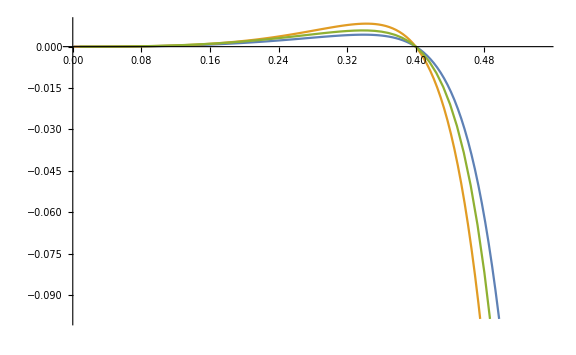

```mathematica
ListPlot[{Z0[0.8],Z2[0.8],ZBCP[0.8]},Joined->True,ImageSize->Large]
```

```mathematica
Clear@curve;
curve[𝒥_]:=Table[{ω,Interpolation[Z0[𝒥]⟦23;;⟧][ω]/Interpolation[DeleteCases[ZBCP[𝒥]⟦10;;⟧,{ω_,Z_}/;Chop[Z]==0]][ω]},{ω,DeleteCases[Range[0.1,0.54,0.004],ω_/;Abs[ω-𝒥/2]<0.01]}]
```

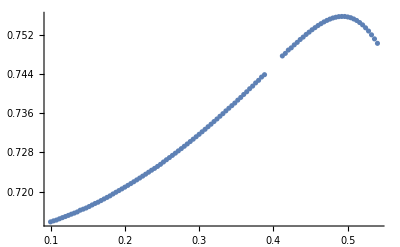

```mathematica
curve[0.8]//ListPlot
```